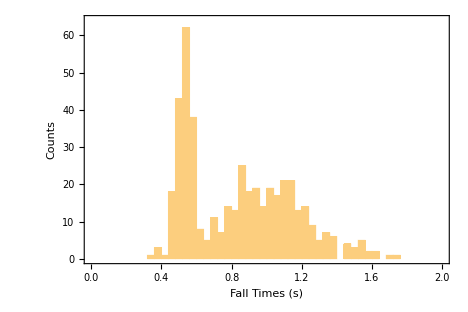

0.843533

0.304514

```mathematica
x0=0.53;
sigma0=0.04;
x1=0.98;
sigma1=0.24;
bins = Table[i,{i,0,2.4,0.04}];
t1=RandomReal[NormalDistribution[x0,sigma0],150];
t2=RandomReal[NormalDistribution[x1,sigma1],300];
t3=Join[t1,t2];
p1=Histogram[t3,{0,2.4,0.04},PlotRange->{{0,2.0},{0,64}},
Frame->True,FrameStyle->Thick, FrameTicksStyle-> Thick, FrameLabel->{"Fall Times (s)","Counts"},
PlotRangePadding->0,
LabelStyle->FontSize->18,
AspectRatio->1/1.5,
ImageSize->6.5*72]
Mean[t3]
StandardDeviation[t3]
```

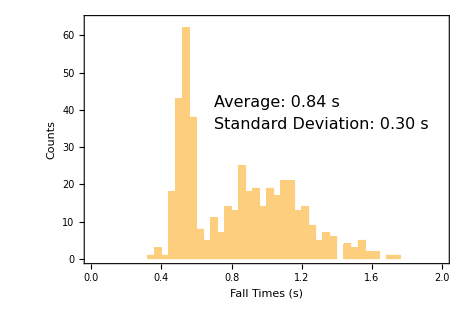

```mathematica
p2 = Show[p1,
Graphics[Text[Style["Average: 0.84 s",16],{0.7,42.0},{-1,0}] ],
Graphics[Text[Style["Standard Deviation: 0.30 s",16],{0.7,36.0},{-1,0} ]]
]
```

```mathematica
"/media/flash/131f08/labs/f08/SampleHist1.eps"
```

/media/flash/131f08/labs/f08/SampleHist1.eps

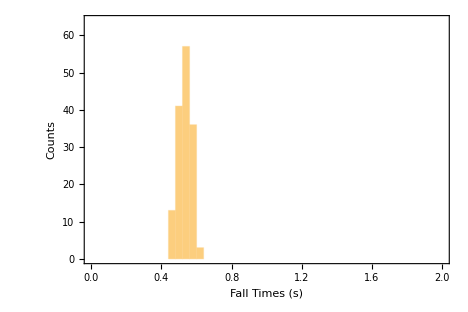

```mathematica
p3=Histogram[t1,{0,2.4,0.04},PlotRange->{{0,2.0},{0,64}},
Frame->True,FrameStyle->Thick, FrameTicksStyle-> Thick, FrameLabel->{"Fall Times (s)","Counts"},
PlotRangePadding->0,
LabelStyle->FontSize->18,
AspectRatio->1/1.5,
ImageSize->6.5*72]
```

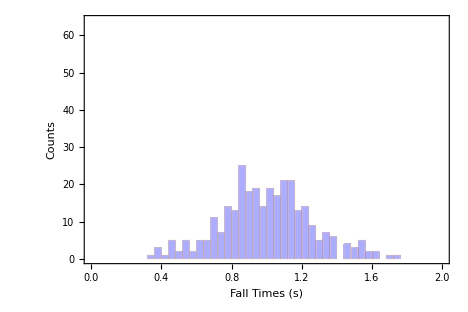

```mathematica
p4=Histogram[Style[t2,RGBColor[0.2,0.2,1.0]],{0,2.4,0.04},
ChartStyle->Opacity[0.4],PlotRange->{{0,2.0},{0,64}},
Frame->True,FrameStyle->Thick, FrameTicksStyle-> Thick, FrameLabel->{"Fall Times (s)","Counts"},
PlotRangePadding->0,
LabelStyle->FontSize->18,
AspectRatio->1/1.5,
ImageSize->6.5*72]
```

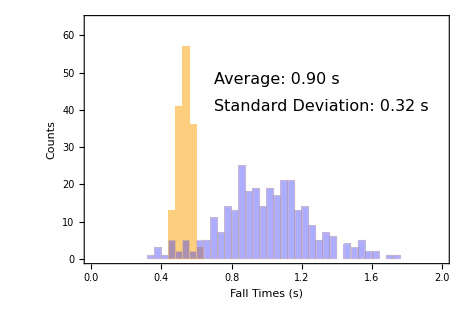

```mathematica
p5 = Show[p3,p4,
Graphics[Text[Style["Average: 0.90 s",16],{0.7,48.0},{-1,0}] ],
Graphics[Text[Style["Standard Deviation: 0.32 s",16],{0.7,41.0},{-1,0} ]]
]
```

```mathematica
Export["/run/media/gilfoyle/KINGSTON/131f19/labManuals/fall2019/131/StudentGuideModule1/measurement_uncertainty/histogram_color.eps",p5]
```

/run/media/gilfoyle/KINGSTON/131f19/labManuals/fall2019/131/StudentGuideModule1/measurement_uncertainty/histogram_color.eps